## NTissueCells-example.nb NTissueCells,NTissueEdges,NTissueVertices

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Sat 10 Nov 2012 08:47:29
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

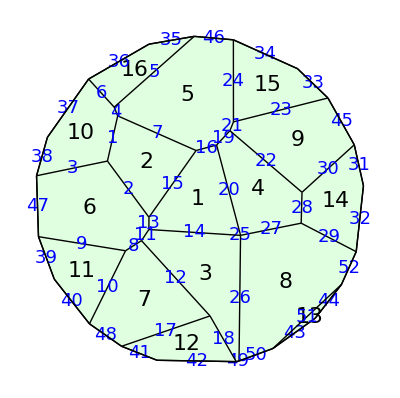

```mathematica
w=TemplateRandomCircularGrid[16,100];
ShowTissue[w, "CellNumbers"-> True, 
"CellNumberStyle"-> {FontSize-> 22}, 
"EdgeNumbers"-> True, "EdgeNumberStyle"-> {Blue, Background-> Pink, FontFamily-> "Verdana", FontSize-> 18}]
```

```mathematica
NTissueCells[w]
```

16

```mathematica
NTissueVertices[w]
```

37

```mathematica
NTissueEdges[w]
```

52

```mathematica
w
```

Tissue[{{-55.7861,24.2544},{-51.6905,56.9757},{-49.5676,51.6893},{-44.8174,-30.1652},{-35.1271,-24.0184},{-30.6561,-17.2723},{-30.5945,-9.8348},{-1.98616,30.6588},{6.46201,-69.7298},{10.45,34.0149},{18.5261,42.6879},{20.6729,48.0391},{24.9791,-20.833},{24.9981,-20.8128},{61.7765,-13.4386},{62.2818,5.32076},{99.5665,9.30118},{59.5407,80.3424},{-30.6001,95.2031},{-92.2153,38.6826},{-88.0682,-47.3707},{-25.706,-96.6395},{70.3433,-71.0761},{93.9921,34.1391},{78.0303,62.5402},{20.6315,97.8486},{-3.14552,99.9505},{-67.227,74.0306},{-98.8151,15.3484},{-97.6332,-21.6275},{-66.7039,-74.5023},{-47.217,-88.1507},{22.3424,-97.4721},{24.0528,-97.0642},{44.5831,-89.5117},{86.2214,-50.6544},{95.1605,-30.7324}},{{1,3},{1,7},{1,29},{2,3},{2,27},{2,28},{3,8},{4,5},{4,30},{4,31},{5,6},{5,9},{6,7},{6,13},{7,8},{8,10},{9,32},{9,33},{10,11},{10,14},{11,12},{11,16},{12,25},{12,26},{13,14},{13,34},{14,15},{15,16},{15,37},{16,24},{17,24},{17,37},{18,25},{18,26},{19,27},{19,28},{20,28},{20,29},{21,30},{21,31},{22,32},{22,33},{23,35},{23,36},{24,25},{26,27},{29,30},{31,32},{33,34},{34,35},{35,36},{36,37}},{{15,13,14,25,20,16},{2,15,7,1},{49,26,14,11,12,18},{20,27,28,22,19},{46,5,4,7,16,19,21,24},{47,9,8,11,13,2,3},{48,17,12,8,10},{52,29,27,25,26,50,51},{45,23,21,22,30},{38,3,1,4,6,37},{40,10,9,39},{42,18,17,41},{44,51,43},{30,28,29,32,31},{34,24,23,33},{36,6,5,35}}]